Simple Model  of a Neuron

Exercise 4: Chain of coupled FHN oscillators

```mathematica
ss1 = {a -> -1,b -> 0.12,c -> 0, e -> 1, r -> 0.12, d -> 0.2};
```

```mathematica
f[v_,w_]=((a - v[t])(v[t] -1) v[t] -w[t])/e + - 2 d v[t] /. ss1;
g[v_,w_]=b v[t] - r w[t] + c /. ss1;
```

```mathematica
d = 0.2;
```

```mathematica
sol = NDSolve[{{v1'[t]==f[v1,w1] + d v2[t], v2'[t]==f[v2,w2]  + d v1[t] + d v3[t], v3'[t]==f[v3,w3]  + d v2[t] + d v4[t], v4'[t]==f[v4,w4]  + d v3[t] + d v5[t],
v5'[t]==f[v5,w5]  + d v4[t] + d v6[t], v6'[t]==f[v6,w6]  + d v5[t] + d v7[t], v7'[t]==f[v7,w7]  + d v6[t] + d v8[t],
v8'[t]==f[v8,w8]  + d v7[t] },{w1'[t]==g[v1,w1], w2'[t]==g[v2,w2],w3'[t]==g[v3,w3], w4'[t]==g[v4,w4],w5'[t]==g[v5,w5],w6'[t]==g[v6,w6], w7'[t]==g[v7,w7],w8'[t]==g[v8,w8]},v1[0]==v2[0] ==v3[0]==v4[0] ==v5[0] == v6[0]==v7[0] ==v8[0] == RandomReal[], w1[0]==w2[0] ==w3[0]==w4[0] ==w5[0] == w6[0]==w7[0] ==w8[0] == RandomReal[]},{v1,v2,v3,v4,v5,v6,v7,v8,w1, w2,w3,w4,w5,w6,w7,w8},{t,100}]
```

{{v1→InterpolatingFunction[…],v2→InterpolatingFunction[…],v3→InterpolatingFunction[…],v4→InterpolatingFunction[…],v5→InterpolatingFunction[…],v6→InterpolatingFunction[…],v7→InterpolatingFunction[…],v8→InterpolatingFunction[…],w1→InterpolatingFunction[…],w2→InterpolatingFunction[…],w3→InterpolatingFunction[…],w4→InterpolatingFunction[…],w5→InterpolatingFunction[…],w6→InterpolatingFunction[…],w7→InterpolatingFunction[…],w8→InterpolatingFunction[…]}}

```mathematica
(*Evaluate[(v1[t]/.sol)/.t->5.]*)
```

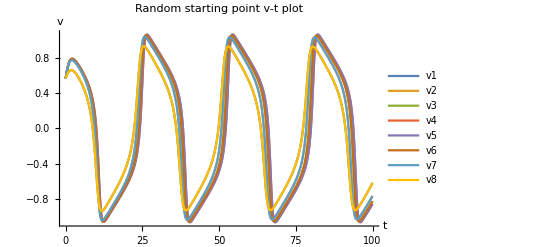

```mathematica
Plot[Evaluate[{v1[t] /. sol,v2[t] /. sol, v3[t] /. sol, v4[t] /. sol, v5[t] /. sol,v6[t] /. sol,v7[t] /. sol, v8[t] /. sol}], {t,0,100}, PlotRange->All, PlotLegends->{"v1","v2","v3","v4","v5","v6","v7","v8"}, AxesLabel->{t,v}, PlotLabel->"Random starting point v-t plot"]
```

```mathematica
vvv1 = Evaluate[(v1[t]/.sol)/.t->Range[50]];
vvv2 = Evaluate[(v2[t]/.sol)/.t->Range[50]];
vvv3 = Evaluate[(v3[t]/.sol)/.t->Range[50]];
vvv4 = Evaluate[(v4[t]/.sol)/.t->Range[50]];
vvv5 = Evaluate[(v5[t]/.sol)/.t->Range[50]];
vvv6 = Evaluate[(v6[t]/.sol)/.t->Range[50]];
vvv7 = Evaluate[(v7[t]/.sol)/.t->Range[50]];
vvv8 = Evaluate[(v8[t]/.sol)/.t->Range[50]];
```

```mathematica
matri = {Flatten[vvv1],Flatten[vvv2],Flatten[vvv3],Flatten[vvv4], Flatten[vvv5],Flatten[vvv6],Flatten[vvv7],Flatten[vvv8]};
```

```mathematica
matri//MatrixForm
```

(0.645458 | 0.663295 | 0.639026 | 0.59109 | 0.527692 | 0.448641 | 0.345618 | 0.195206 | -0.0624966 | -0.50886 | -0.881749 | -0.938719 | -0.896576 | -0.839102 | -0.77858 | -0.716149 | -0.650923 | -0.58096 | -0.502728 | -0.409336 | -0.285822 | -0.0962232 | 0.237945 | 0.702079 | 0.924328 | 0.925586 | 0.875889 | 0.817394 | 0.756468 | 0.693417 | 0.627062 | 0.555085 | 0.473206 | 0.372833 | 0.234748 | 0.012662 | -0.374438 | -0.797842 | -0.932937 | -0.912511 | -0.859698 | -0.800646 | -0.739345 | -0.675674 | -0.608221 | -0.534306 | -0.448889 | -0.341606 | -0.188722 | 0.0660276
0.732687 | 0.777318 | 0.756725 | 0.710621 | 0.651866 | 0.581646 | 0.493902 | 0.370283 | 0.155766 | -0.307129 | -0.918322 | -1.04791 | -1.01043 | -0.955082 | -0.897728 | -0.839566 | -0.779985 | -0.717663 | -0.650271 | -0.573356 | -0.477265 | -0.337334 | -0.0794967 | 0.467116 | 0.976218 | 1.04172 | 0.999134 | 0.943488 | 0.886073 | 0.827732 | 0.767743 | 0.704632 | 0.635744 | 0.555875 | 0.453322 | 0.296953 | -0.0075953 | -0.610126 | -1.00609 | -1.034 | -0.988016 | -0.932114 | -0.874615 | -0.816062 | -0.755621 | -0.691643 | -0.621114 | -0.537961 | -0.428058 | -0.252423
0.73995 | 0.791449 | 0.773292 | 0.728966 | 0.673107 | 0.608085 | 0.530061 | 0.426677 | 0.261455 | -0.0879781 | -0.772844 | -1.05944 | -1.03754 | -0.983624 | -0.92724 | -0.870532 | -0.813168 | -0.754243 | -0.69223 | -0.624387 | -0.545179 | -0.441517 | -0.275401 | 0.0826099 | 0.773022 | 1.05765 | 1.03798 | 0.984373 | 0.92798 | 0.871216 | 0.81377 | 0.754724 | 0.692507 | 0.62426 | 0.544103 | 0.437714 | 0.26192 | -0.129248 | -0.818904 | -1.05777 | -1.03377 | -0.97997 | -0.92356 | -0.866742 | -0.809164 | -0.74986 | -0.687154 | -0.617944 | -0.535689 | -0.42388
0.740392 | 0.792899 | 0.77538 | 0.731547 | 0.676394 | 0.612659 | 0.537235 | 0.439812 | 0.291022 | -0.00636259 | -0.656859 | -1.0528 | -1.04671 | -0.993801 | -0.937583 | -0.881122 | -0.824219 | -0.766106 | -0.70551 | -0.640234 | -0.566071 | -0.473751 | -0.338583 | -0.0781201 | 0.535915 | 1.03928 | 1.05489 | 1.00323 | 0.946962 | 0.890408 | 0.833476 | 0.775436 | 0.715071 | 0.650276 | 0.577029 | 0.48643 | 0.354464 | 0.098859 | -0.516783 | -1.03779 | -1.05612 | -1.0045 | -0.948171 | -0.891546 | -0.834535 | -0.776401 | -0.715906 | -0.650899 | -0.577221 | -0.485499
0.740392 | 0.792899 | 0.77538 | 0.731547 | 0.676394 | 0.612659 | 0.537235 | 0.439812 | 0.291022 | -0.00636259 | -0.656859 | -1.0528 | -1.04671 | -0.993801 | -0.937583 | -0.881122 | -0.824219 | -0.766106 | -0.70551 | -0.640234 | -0.566071 | -0.473751 | -0.338583 | -0.0781201 | 0.535915 | 1.03928 | 1.05489 | 1.00323 | 0.946962 | 0.890408 | 0.833476 | 0.775436 | 0.715071 | 0.650276 | 0.577029 | 0.48643 | 0.354464 | 0.098859 | -0.516783 | -1.03779 | -1.05612 | -1.0045 | -0.948171 | -0.891546 | -0.834535 | -0.776401 | -0.715906 | -0.650899 | -0.577221 | -0.485499
0.73995 | 0.791449 | 0.773292 | 0.728966 | 0.673107 | 0.608085 | 0.530061 | 0.426677 | 0.261455 | -0.0879781 | -0.772844 | -1.05944 | -1.03754 | -0.983624 | -0.92724 | -0.870532 | -0.813168 | -0.754243 | -0.69223 | -0.624387 | -0.545179 | -0.441517 | -0.275401 | 0.0826099 | 0.773022 | 1.05765 | 1.03798 | 0.984373 | 0.92798 | 0.871216 | 0.81377 | 0.754724 | 0.692507 | 0.62426 | 0.544103 | 0.437714 | 0.26192 | -0.129248 | -0.818904 | -1.05777 | -1.03377 | -0.97997 | -0.92356 | -0.866742 | -0.809164 | -0.74986 | -0.687154 | -0.617944 | -0.535689 | -0.42388
0.732687 | 0.777318 | 0.756725 | 0.710621 | 0.651866 | 0.581646 | 0.493902 | 0.370283 | 0.155766 | -0.307129 | -0.918322 | -1.04791 | -1.01043 | -0.955082 | -0.897728 | -0.839566 | -0.779985 | -0.717663 | -0.650271 | -0.573356 | -0.477265 | -0.337334 | -0.0794967 | 0.467116 | 0.976218 | 1.04172 | 0.999134 | 0.943488 | 0.886073 | 0.827732 | 0.767743 | 0.704632 | 0.635744 | 0.555875 | 0.453322 | 0.296953 | -0.0075953 | -0.610126 | -1.00609 | -1.034 | -0.988016 | -0.932114 | -0.874615 | -0.816062 | -0.755621 | -0.691643 | -0.621114 | -0.537961 | -0.428058 | -0.252423
0.645458 | 0.663295 | 0.639026 | 0.59109 | 0.527692 | 0.448641 | 0.345618 | 0.195206 | -0.0624966 | -0.50886 | -0.881749 | -0.938719 | -0.896576 | -0.839102 | -0.77858 | -0.716149 | -0.650923 | -0.58096 | -0.502728 | -0.409336 | -0.285822 | -0.0962232 | 0.237945 | 0.702079 | 0.924328 | 0.925586 | 0.875889 | 0.817394 | 0.756468 | 0.693417 | 0.627062 | 0.555085 | 0.473206 | 0.372833 | 0.234748 | 0.012662 | -0.374438 | -0.797842 | -0.932937 | -0.912511 | -0.859698 | -0.800646 | -0.739345 | -0.675674 | -0.608221 | -0.534306 | -0.448889 | -0.341606 | -0.188722 | 0.0660276)

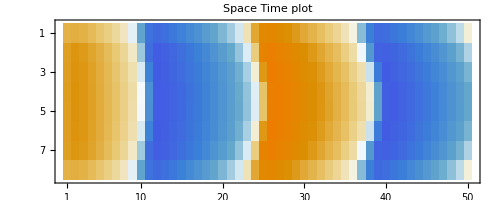

```mathematica
MatrixPlot[matri, PlotLabel->"Space Time plot"]
```

The above plot is the space time plot, with the horizontal axis denoting time [1,50], while the vertical axis is the value of v_i at time t. v1 is shown on the first row, then ... until v8 on the last row. Blue is negative, and yellowish orange is positive, with the darker the color, the larger the value.

```mathematica
Clear[v1,v2,v3,v4,v5,v6,v7,v8,w1,w2,w3,w4,w5,w6,w7,w8]
```

```mathematica
ptt = NSolve[{((-1 - v1)(v1 -1) v1 -w1)/1 - 0.4 v1 + 0.2 v2== 0,((-1 - v2)(v2 -1) v2 -w2)/1 - 0.4 v2 + 0.2 v3 + 0.2 v1== 0,
((-1 - v3)(v3 -1) v3 -w3)/1 - 0.4 v3 + 0.2 v4 + 0.2 v2== 0,((-1 - v4)(v4 -1) v4 -w4)/1 - 0.4 v4 + 0.2 v5 + 0.2 v3== 0,
((-1 - v5)(v5 -1) v5 -w5)/1 - 0.4 v5 + 0.2 v6 + 0.2 v4== 0,
((-1 - v6)(v6 -1) v6 -w6)/1 - 0.4 v6 + 0.2 v7 + 0.2 v5== 0,((-1 - v7)(v7 -1) v7 -w7)/1 - 0.4 v7 + 0.2 v8 + 0.2 v6== 0,
((-1 - v8)(v8 -1) v8 -w8)/1 - 0.4 v8 + 0.2 v7 == 0,  0.12 v1 -0.12 w1 == 0,0.12 v2 -0.12 w2 == 0, 0.12 v3 -0.12 w3 == 0,0.12 v4 -0.12 w4 == 0, 0.12 v5 -0.12 w5 == 0,0.12 v6 -0.12 w6 == 0,0.12 v7 -0.12 w7 == 0, 0.12 v8 -0.12 w8 == 0},{v1,v2,v3,v4,v5,v6,v7,v8,w1,w2,w3,w4,w5,w6,w7,w8}]
```

{{v1→0.-0.789797 ⅈ,v2→0.+0.883702 ⅈ,v3→0.-0.893341 ⅈ,10,w6→0.+0.893341 ⅈ,w7→0.-0.883702 ⅈ,w8→0.+0.789797 ⅈ},6559,{v1→0,14,w8→0}}
 |  |  |  |

```mathematica
Clear[v1,v2,v3,v4,v5,v6,v7,v8,w1,w2,w3,w4,w5,w6,w7,w8,t]
```

```mathematica
soll = NDSolve[{{v1'[t]==f[v1,w1] + d v2[t], v2'[t]==f[v2,w2]  + d v1[t] + d v3[t], v3'[t]==f[v3,w3]  + d v2[t] + d v4[t], v4'[t]==f[v4,w4]  + d v3[t] + d v5[t],
v5'[t]==f[v5,w5]  + d v4[t] + d v6[t], v6'[t]==f[v6,w6]  + d v5[t] + d v7[t], v7'[t]==f[v7,w7]  + d v6[t] + d v8[t],
v8'[t]==f[v8,w8]  + d v7[t] },{w1'[t]==g[v1,w1], w2'[t]==g[v2,w2],w3'[t]==g[v3,w3], w4'[t]==g[v4,w4],w5'[t]==g[v5,w5],w6'[t]==g[v6,w6], w7'[t]==g[v7,w7],w8'[t]==g[v8,w8]},{v1[0]==0., v2[0] ==0.,v3[0]==0.,v4[0] ==0.,v5[0] ==0.3,v6[0]==0.,v7[0] ==0.,v8[0] == 0.}, {w1[0]==0.,w2[0] ==0.,w3[0]==0., w4[0] ==0., w5[0] == 0., w6[0]==0., w7[0] ==0.,w8[0] == 0.}},{v1,v2,v3,v4,v5,v6,v7,v8,w1, w2,w3,w4,w5,w6,w7,w8},{t,100}]
```

{{v1→InterpolatingFunction[…],v2→InterpolatingFunction[…],v3→InterpolatingFunction[…],v4→InterpolatingFunction[…],v5→InterpolatingFunction[…],v6→InterpolatingFunction[…],v7→InterpolatingFunction[…],v8→InterpolatingFunction[…],w1→InterpolatingFunction[…],w2→InterpolatingFunction[…],w3→InterpolatingFunction[…],w4→InterpolatingFunction[…],w5→InterpolatingFunction[…],w6→InterpolatingFunction[…],w7→InterpolatingFunction[…],w8→InterpolatingFunction[…]}}

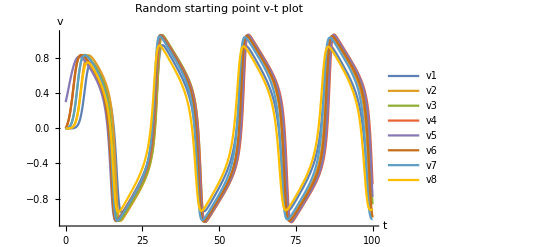

```mathematica
Plot[Evaluate[{v1[t] /. soll,v2[t] /. soll, v3[t] /. soll, v4[t] /. soll, v5[t] /. soll,v6[t] /. soll,v7[t] /. soll, v8[t] /. soll}], {t,0,100}, PlotRange->All, PlotLegends->{"v1","v2","v3","v4","v5","v6","v7","v8"}, AxesLabel->{t,v}, PlotLabel->"Random starting point v-t plot"]
```

```mathematica
vv1 = Evaluate[(v1[t]/.soll)/.t->Range[50]];
vv2 = Evaluate[(v2[t]/.soll)/.t->Range[50]];
vv3 = Evaluate[(v3[t]/.soll)/.t->Range[50]];
vv4 = Evaluate[(v4[t]/.soll)/.t->Range[50]];
vv5 = Evaluate[(v5[t]/.soll)/.t->Range[50]];
vv6 = Evaluate[(v6[t]/.soll)/.t->Range[50]];
vv7 = Evaluate[(v7[t]/.soll)/.t->Range[50]];
vv8 = Evaluate[(v8[t]/.soll)/.t->Range[50]];
```

```mathematica
matri = {Flatten[vv1],Flatten[vv2],Flatten[vv3],Flatten[vv4], Flatten[vv5],Flatten[vv6],Flatten[vv7],Flatten[vv8]};
```

```mathematica
matri//MatrixForm
```

(0.0000352666 | 0.000968614 | 0.00818378 | 0.0413016 | 0.14765 | 0.375507 | 0.632913 | 0.744536 | 0.740582 | 0.695039 | 0.634111 | 0.562852 | 0.478111 | 0.368297 | 0.200462 | -0.126251 | -0.696817 | -0.949932 | -0.933604 | -0.878326 | -0.818054 | -0.756066 | -0.691901 | -0.624027 | -0.549665 | -0.463536 | -0.354441 | -0.195322 | 0.0839105 | 0.572204 | 0.918164 | 0.941259 | 0.891846 | 0.832866 | 0.771743 | 0.708736 | 0.642691 | 0.571412 | 0.490881 | 0.393073 | 0.259981 | 0.0470531 | -0.335794 | -0.794901 | -0.941996 | -0.916929 | -0.861975 | -0.80217 | -0.740487 | -0.676491
0.000700812 | 0.00952484 | 0.0524628 | 0.186861 | 0.456284 | 0.722688 | 0.82545 | 0.827166 | 0.790412 | 0.738241 | 0.677345 | 0.607244 | 0.521774 | 0.403044 | 0.192721 | -0.298872 | -0.940726 | -1.05162 | -1.01115 | -0.955449 | -0.897943 | -0.839628 | -0.779859 | -0.717291 | -0.649547 | -0.572061 | -0.474852 | -0.33196 | -0.061667 | 0.537628 | 1.02282 | 1.04365 | 0.992815 | 0.935896 | 0.878115 | 0.819442 | 0.758963 | 0.695054 | 0.624803 | 0.542431 | 0.434688 | 0.265373 | -0.0784132 | -0.731384 | -1.04289 | -1.03048 | -0.977243 | -0.920128 | -0.862225 | -0.803234
0.0103773 | 0.0686061 | 0.235095 | 0.525018 | 0.760681 | 0.83596 | 0.829073 | 0.791244 | 0.740802 | 0.682951 | 0.617472 | 0.539924 | 0.437962 | 0.274952 | -0.0733283 | -0.741728 | -1.04422 | -1.03803 | -0.987181 | -0.931396 | -0.874938 | -0.817845 | -0.759348 | -0.698077 | -0.631619 | -0.555301 | -0.458709 | -0.313993 | -0.0300218 | 0.605073 | 1.04498 | 1.04954 | 0.997524 | 0.941272 | 0.88465 | 0.827537 | 0.769161 | 0.708211 | 0.642414 | 0.567394 | 0.473492 | 0.335088 | 0.0683196 | -0.547479 | -1.03869 | -1.05306 | -1.00144 | -0.945115 | -0.888417 | -0.831248
0.10105 | 0.312269 | 0.600409 | 0.787018 | 0.836509 | 0.821929 | 0.782197 | 0.731697 | 0.674592 | 0.61061 | 0.536079 | 0.441544 | 0.301963 | 0.0406535 | -0.516693 | -0.99497 | -1.04757 | -1.00544 | -0.95118 | -0.895396 | -0.839152 | -0.782023 | -0.723034 | -0.660525 | -0.591524 | -0.510086 | -0.40246 | -0.230407 | 0.128716 | 0.794378 | 1.0587 | 1.03656 | 0.983008 | 0.926934 | 0.870601 | 0.813741 | 0.755552 | 0.6947 | 0.628876 | 0.553655 | 0.459301 | 0.320129 | 0.0525245 | -0.560484 | -1.0407 | -1.05324 | -1.00157 | -0.945396 | -0.888927 | -0.832086
0.467493 | 0.633768 | 0.756348 | 0.814113 | 0.813433 | 0.78162 | 0.735896 | 0.682726 | 0.623337 | 0.55586 | 0.474746 | 0.36657 | 0.195503 | -0.141879 | -0.742171 | -1.04103 | -1.03726 | -0.987191 | -0.932005 | -0.876177 | -0.819881 | -0.762484 | -0.702854 | -0.639074 | -0.567634 | -0.481306 | -0.362769 | -0.162024 | 0.274035 | 0.914689 | 1.06156 | 1.0244 | 0.969716 | 0.913608 | 0.857249 | 0.80022 | 0.74162 | 0.679953 | 0.612576 | 0.534265 | 0.433051 | 0.275563 | -0.0508412 | -0.725886 | -1.05708 | -1.04268 | -0.989436 | -0.933236 | -0.876773 | -0.819812
0.10105 | 0.312268 | 0.600402 | 0.786968 | 0.836318 | 0.821466 | 0.781366 | 0.730369 | 0.672534 | 0.607418 | 0.530938 | 0.432525 | 0.283694 | -0.0040278 | -0.606106 | -1.02906 | -1.04671 | -0.997586 | -0.942026 | -0.885778 | -0.829055 | -0.771199 | -0.711029 | -0.646524 | -0.573922 | -0.485299 | -0.36102 | -0.141919 | 0.351195 | 0.968693 | 1.06059 | 1.01664 | 0.961169 | 0.904749 | 0.847981 | 0.790295 | 0.730615 | 0.667116 | 0.596425 | 0.511468 | 0.394701 | 0.192479 | -0.267517 | -0.922114 | -1.06051 | -1.02299 | -0.968116 | -0.911695 | -0.85489 | -0.797209
0.0103772 | 0.0686008 | 0.234995 | 0.524276 | 0.758145 | 0.830772 | 0.821283 | 0.780493 | 0.726565 | 0.664387 | 0.592679 | 0.504602 | 0.381382 | 0.165075 | -0.323581 | -0.94849 | -1.05116 | -1.00932 | -0.953485 | -0.896032 | -0.837801 | -0.778134 | -0.715699 | -0.648157 | -0.571063 | -0.474817 | -0.334986 | -0.0773454 | 0.482167 | 1.00001 | 1.04522 | 0.997407 | 0.940933 | 0.88334 | 0.824898 | 0.764787 | 0.701491 | 0.632319 | 0.551999 | 0.44871 | 0.291018 | -0.0172016 | -0.631019 | -1.01935 | -1.03512 | -0.986118 | -0.92971 | -0.872097 | -0.813469 | -0.752921
0.000699393 | 0.00944611 | 0.0514489 | 0.179989 | 0.429159 | 0.668197 | 0.750163 | 0.73406 | 0.68446 | 0.62148 | 0.548155 | 0.460152 | 0.343971 | 0.161987 | -0.193257 | -0.751245 | -0.952281 | -0.927189 | -0.871028 | -0.810634 | -0.748545 | -0.684179 | -0.615928 | -0.540887 | -0.453524 | -0.342079 | -0.178265 | 0.108949 | 0.591568 | 0.916213 | 0.938454 | 0.889762 | 0.831052 | 0.770063 | 0.707163 | 0.641233 | 0.570111 | 0.489843 | 0.392579 | 0.260864 | 0.0520861 | -0.319319 | -0.773611 | -0.936157 | -0.918244 | -0.865038 | -0.805752 | -0.744379 | -0.680742 | -0.613434)

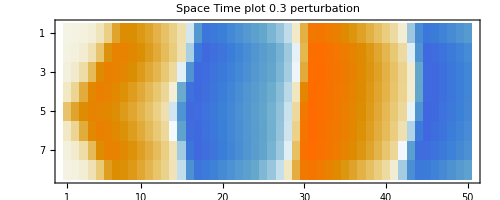

```mathematica
MatrixPlot[matri, PlotLabel->"Space Time plot 0.3 perturbation"]
```

The above plot is the space time plot, with the horizontal axis denoting time [1,50], while the vertical axis is the value of v_i at time t. v1 is shown on the first row, then ... until v8 on the last row. Blue is negative, and yellowish orange is positive, with the darker the color, the larger the value. Here in the plot, there is a perturbation in v5, thus we can see that v5 has a large value at time t = 1, and then it affects v4 and v6, then affects v3 and v7, etc. This chain of coupled FHN oscillator shows that the activation of one neuron, will affect neighboring neurons. Compared with the plot generated with random number, except the first period, the later parts look quite similar.

Exercise 5: Spiral waves in a simple model of excitable dynamics

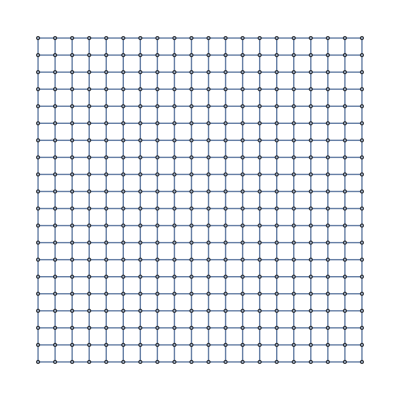

```mathematica
grgr = GridGraph[{20,20}]
```

2 stands for E, excitatory
1 stands for R, refractory
0 stands for S, susceptible

```mathematica
ini = Join[ConstantArray[0,160],ConstantArray[1,10],ConstantArray[0,10],ConstantArray[2,10],ConstantArray[0,210]]
```

{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,1,1,1,1,1,1,1,1,1,0,0,0,0,0,0,0,0,0,0,2,2,2,2,2,2,2,2,2,2,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}

The initial setup, as indicated in the task. (10,1), ...(10,10) set to E, (9,1),...(9,10) set to R

```mathematica
adj = Normal[AdjacencyMatrix[grgr]]
```

{1}
 |  |  |  |

```mathematica
updateState[vec_,adj_]:= Module[{a1,a2},a1 = adj . ((vec /. 1-> 0)/2);a2 = Table[If[vec[[i]] == 0 && a1[[i]] >0, 2, If[vec[[i]] == 2, 1,0]],{i,1,400}]]
```

```mathematica
(*Here, apply the three rules: S -> E if in neighborhood, E-> R R -> S. In order to check the neighborhood, the dot product of the adjacency matrix and only excitatory states is computed in a1*)
```

```mathematica
ini
```

{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,1,1,1,1,1,1,1,1,1,0,0,0,0,0,0,0,0,0,0,2,2,2,2,2,2,2,2,2,2,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}

```mathematica
r1 = updateState[ini,adj];
r2 = updateState[r1,adj];
r3 = updateState[r2,adj];
r4 = updateState[r3,adj];
r5 = updateState[r4,adj];
r6 = updateState[r5,adj];
r7 = updateState[r6,adj];
r8 = updateState[r7,adj];
r9 = updateState[r8,adj];
r10 = updateState[r9,adj];
r11 = updateState[r10,adj];
r12 = updateState[r11,adj];
r13 = updateState[r12,adj];
r14 = updateState[r13,adj];
r15 = updateState[r14,adj];
```

The below section shows the pattern. Black nodes denote Refractory, and Red denote Excitatory, all others are Susceptible

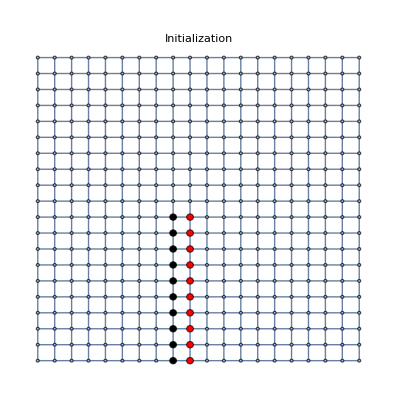

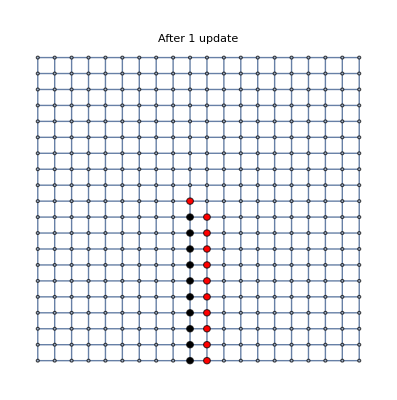

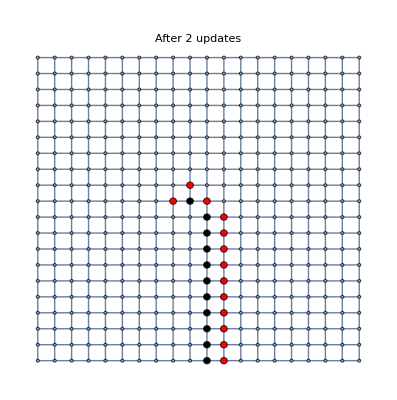

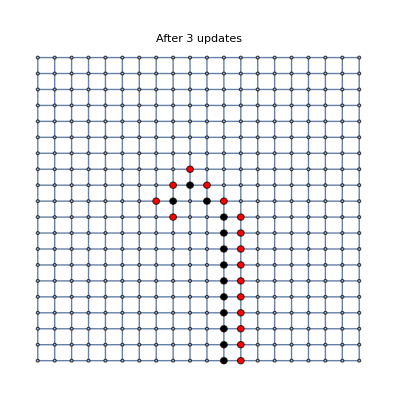

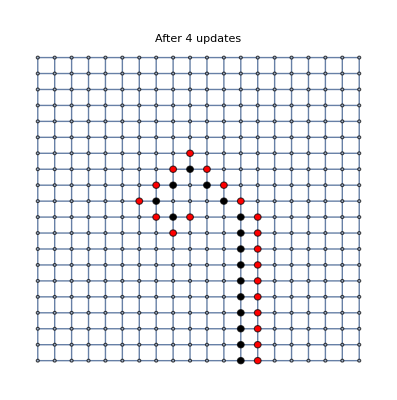

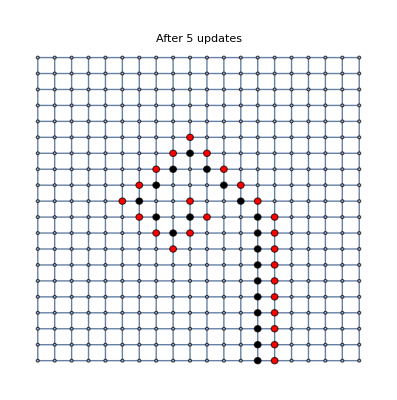

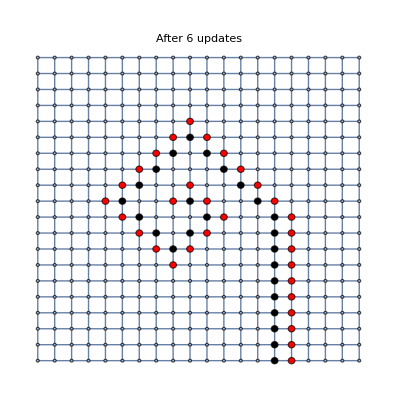

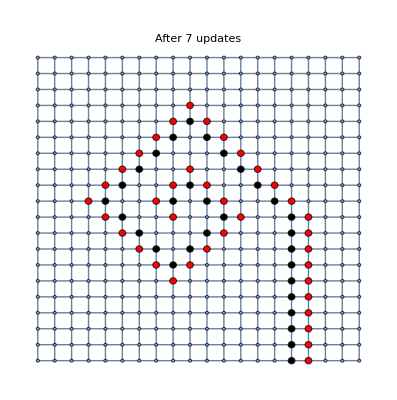

```mathematica
HighlightGraph[GridGraph[{20,20}],{Style[Flatten[Position[ini,1]],Black], Style[Flatten[Position[ini,2]],Red]},VertexSize->.4, PlotLabel->"Initialization"]

HighlightGraph[GridGraph[{20,20}],{Style[Flatten[Position[r1,1]],Black], Style[Flatten[Position[r1,2]],Red]},VertexSize->.4,PlotLabel->"After 1 update"]

HighlightGraph[GridGraph[{20,20}],{Style[Flatten[Position[r2,1]],Black], Style[Flatten[Position[r2,2]],Red]},VertexSize->.4, PlotLabel->"After 2 updates"]

HighlightGraph[GridGraph[{20,20}],{Style[Flatten[Position[r3,1]],Black], Style[Flatten[Position[r3,2]],Red]},VertexSize->.4,PlotLabel->"After 3 updates"]

HighlightGraph[GridGraph[{20,20}],{Style[Flatten[Position[r4,1]],Black], Style[Flatten[Position[r4,2]],Red]},VertexSize->.4,PlotLabel->"After 4 updates"]

HighlightGraph[GridGraph[{20,20}],{Style[Flatten[Position[r5,1]],Black], Style[Flatten[Position[r5,2]],Red]},VertexSize->.4,PlotLabel->"After 5 updates"]

HighlightGraph[GridGraph[{20,20}],{Style[Flatten[Position[r6,1]],Black], Style[Flatten[Position[r6,2]],Red]},VertexSize->.4,PlotLabel->"After 6 updates"]

HighlightGraph[GridGraph[{20,20}],{Style[Flatten[Position[r7,1]],Black], Style[Flatten[Position[r7,2]],Red]},VertexSize->.4,PlotLabel->"After 7 updates"]

HighlightGraph[GridGraph[{20,20}],{Style[Flatten[Position[r8,1]],Black], Style[Flatten[Position[r8,2]],Red]},VertexSize->.4, PlotLabel->"After 8 updates"]

HighlightGraph[GridGraph[{20,20}],{Style[Flatten[Position[r9,1]],Black], Style[Flatten[Position[r9,2]],Red]},VertexSize->.4,PlotLabel->"After 9 updates"]

HighlightGraph[GridGraph[{20,20}],{Style[Flatten[Position[r10,1]],Black], Style[Flatten[Position[r10,2]],Red]},VertexSize->.4,
PlotLabel->"After 10 updates"]

HighlightGraph[GridGraph[{20,20}],{Style[Flatten[Position[r11,1]],Black], Style[Flatten[Position[r11,2]],Red]},VertexSize->.4,PlotLabel->"After 11 updates"]

HighlightGraph[GridGraph[{20,20}],{Style[Flatten[Position[r12,1]],Black], Style[Flatten[Position[r12,2]],Red]},VertexSize->.4,PlotLabel->"After 12 updates"]

HighlightGraph[GridGraph[{20,20}],{Style[Flatten[Position[r13,1]],Black], Style[Flatten[Position[r13,2]],Red]},VertexSize->.4,PlotLabel->"After 13 updates"]

HighlightGraph[GridGraph[{20,20}],{Style[Flatten[Position[r14,1]],Black], Style[Flatten[Position[r14,2]],Red]},VertexSize->.4,PlotLabel->"After 14 updates"]

HighlightGraph[GridGraph[{20,20}],{Style[Flatten[Position[r15,1]],Black], Style[Flatten[Position[r15,2]],Red]},VertexSize->.4,PlotLabel->"After 15 updates"]
```

Black nodes denote Refractory, and Red denote Excitatory, all others are Susceptible

According to the above plots, we can see this beautiful spiral waves. This is so because that in the initial condition, the the refractory is as the same number as the excitatory, while they are next to each other, and also with the same number. Then since the probability of R -> S is 1, if the initial pattern is continuous, then the resulting image shall still be continuous. Furthermore, as in S-> E, neighborhood is checked, then it is likely that starting from vertical line, then in the end generates diagonal lines.